FittedModel[0.965915+0.0055139 x]

FittedModel[1.06719+0.0000523647 x^2]

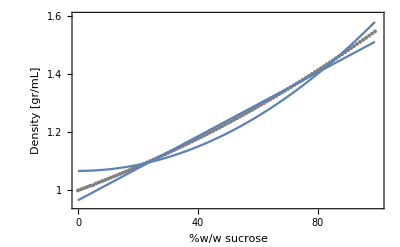

```mathematica
Subscript[ρ, suc]={1000.00,1003.89,1007.79,1011.72,1015.67,1017.85,1023.66,1027.70,1031.76,1035.86,1039.98,1044.13,1048.31,1052.52,1056.77,1061.04,1065.34,1069.68,1074.04,1078.44,1082.87,1087.33,1091.83,1096.36,1100.92,1105.51,1110.14,1114.80,1119.49,1124.22,1128.98,1133.78,1138.61,1143.47,1148.37,1153.31,1158.28,1163.29,1168.33,1173.41,1178.53,1183.68,1188.87,1194.10,1199.36,1204.67,1210.01,1215.38,1220.80,1226.25,1231.74,1237.27,1242.84,1248.44,1254.08,1259.76,1265.48,1271.23,1277.03,1282.86,1288.73,1294.64,1300.59,1306.57,1312.60,1318.66,1324.76,1330.90,1337.08,1343.30,1349.56,1355.85,1362.18,1368.58,1374.96,1381.41,1387.90,1394.42,1400.98,1407.58,1414.21,1420.88,1427.59,1434.34,1441.12,1447.94,1454.80,1461.70,1468.62,1475.59,1482.59,1489.63,1496.71,1503.81,1510.96,1518.14,1525.35,1532.60,1539.88,1547.19}*10^-3; (* U.S.National Bureau of Standard,Circular C440 *)
SucWPer=Range[0,99,1];
lm=LinearModelFit[Subscript[ρ, suc],x,x]
nlm=NonlinearModelFit[Subscript[ρ, suc],b+a x^2,{a,b},x]
Show[ListPlot[Transpose@{SucWPer,Subscript[ρ, suc]},
Frame->True, PlotStyle->Gray, PlotMarkers->{Automatic,4},
FrameLabel->{"%w/w sucrose","Density [gr/mL]"},FrameTicks->{{{1,1.1,1.2,1.3,1.4,1.5,1.6},None},{{0,20,40,60,80,100},None}},
RotateLabel->False,
PlotRange->{{0,100},{0.95,1.6}} 
],
Plot[lm[x],{x,0,99}],
Plot[nlm[x],{x,0,99}]]
```

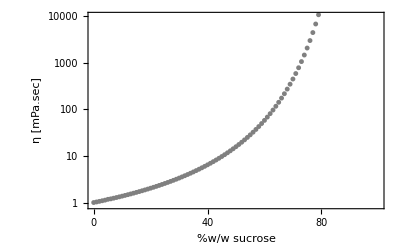

```mathematica
(* Quintas, Brandao, Silva, Cunha 2006 *)
Subscript[x, suc]=(1/342.3)/(1/342.3+((100-SucWPer)/(SucWPer+0.001))/18.01);
Vm=(Subscript[x, suc] 342.3 + (1-Subscript[x, suc]) 18.01)/(SucDen * 10^3);
η=6.31 10^-3 Exp[282*Vm]; (* in Pa.sec *)
ListLogPlot[Transpose@{SucWPer,η},
Frame->True, PlotStyle->Gray, PlotMarkers->{Automatic,5},
FrameLabel->{"%w/w sucrose","η [mPa.sec]"},FrameTicks->{{{0.001,0.01,0.1,1,10,100,1000,10000},None},{{0,20,40,60,80,100},None}},
RotateLabel->False,
PlotRange->{{0,100},{0.9,10^4}} 
]
```

```mathematica
Vm40 = 1/282 Log[1.77/(6.31 10^-3)]
```

0.0199879

```mathematica
ListPlot[Transpose@{SucWPer,η},
Frame->True, 
FrameLabel->{"%w/w sucrose","η [mPa.sec]"},FrameTicks->{{{1,2,3,4,5},None},{{0,5,10,15,20,25,30},None}},
RotateLabel->False,PlotStyle->Gray, PlotMarkers->{Automatic,7},
Epilog->{Directive[Gray,Dashed],Line[{{0,1.77},{40,1.77}}],Line[{{0,1.96},{40,1.96}}],Line[{{0,2.84},{40,2.84}}]},
PlotRange->{{0,30},{0.9,4}} 
]
```

-Graphics-